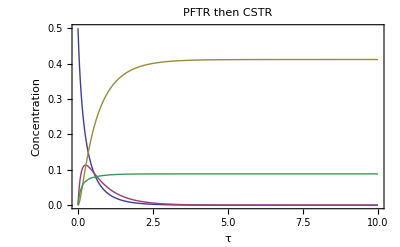

{0.11303,{t→0.250464}}

0.193716 m-xylene

0.106646 o-xylene

0.0672002 d

```mathematica
"PFTR then CSTR";
ClearAll["Global`"]

k1=1.2;
k2=1.5;
k3=1.1;
Cao=0.5;

Solution1=NDSolve[{Ca'[t]==-k1*Ca[t]-k3*Ca[t]^2, Ca[0]==0.5}, Ca, {t,0,20}];
CaPFTR[t_]=Ca[t]/.Flatten[Solution1];
"Plot[CaPFTR[t], {t,0,20}, PlotRange→All]";

Solution2=NDSolve[{Cb'[t]==k1*CaPFTR[t]-k2*Cb[t],Cb[0]==0}, Cb, {t,0,20}];
CbPFTR[t_]=Cb[t]/.Flatten[Solution2];
"Plot[CbPFTR[t],{t,0,20}, PlotRange→All]";

Solution5=NDSolve[{Cc'[t]== k2*CbPFTR[t], Cc[0]== 0},Cc,{t,0,20}];
CcPFTR[t_]=Cc[t]/.Flatten[Solution5];

Solution4=NDSolve[{Cd'[t]==k3*CaPFTR[t]^2, Cd[0]==0}, Cd, {t,0,20}];
CdPFTR[t_]=Cd[t]/.Flatten[Solution4];
"Plot[CdPFTR[t],{t,0,20},PlotRange→All]";

Ca2[t_]=(-1-2*k1*t+√(8*CaPFTR[t]*k3*t+(1+2*k1*t)^2))/(4*k3*t);
Cb2[t_]=(CbPFTR[t]+2*Ca2[t]*t)/(1+2*k2*t);
Cc2[t_]=2*t*k2*Cb2[t]+CcPFTR[t];
Cd2[t_]=CdPFTR[t]+2*k3*t*Ca2[t]^2;


Needs["PlotLegends`"];

Plot[{Ca2[t],Cb2[t],Cc2[t], Cd2[t]},{t,0,10},PlotRange->All,PlotLegend->{"m-xylene", "p-xylene", "o-xylene", "d"}, LegendPosition->{1.1,-0.4}, Frame->True, PlotStyle->{Thick}, PlotLabel->Style["PFTR then CSTR",16],FrameLabel->{"τ","Concentration"}]

FindMaximum[Cb2[t],{t,0,0.1}]
"m-xylene" Ca2[0.250464]
"o-xylene" Cc2[0.250464]
"d" Cd2[0.250464]
```